We want to solve the following equation:

2 ⅇ^(-2 ϵ+2 ψ[τ,σ]) (σ (ψ^(0,1)[τ,σ] (2-3 σ-(-1+σ) σ ψ^(0,1)[τ,σ])-(-1+σ) σ ψ^(0,2)[τ,σ])+(-2 σ+(1-2 σ^2) ψ^(0,1)[τ,σ]) ψ^(1,0)[τ,σ]-(1+σ) (ψ^(1,0)[τ,σ])^2+(1-2 σ^2) ψ^(1,1)[τ,σ]-(1+σ) ψ^(2,0)[τ,σ]) = 0

Lets us x,t in the below instead of τ,σ for convenience,we also only care about the term in brackets,so we have

x ((∂ψ)/(∂x) (2-3 x-(-1+x) x (∂ψ)/(∂x))-(-1+x) x (∂^2 ψ)/(∂^2 x))+(-2 x+(1-2 x^2) (∂ψ)/(∂x)) (∂ψ)/(∂t)-(1+x) ((∂ψ)/(∂t))^2+(1-2 x^2) ∂/(∂x)(((∂ψ)/(∂t)))-(1+x) (∂^2 ψ)/(∂^2 t) = 0

Let multiply out all the terms in the above.

(2x - 3 x^2)(∂ψ)/(∂x)- (-1+x)x^2((∂ψ)/(∂x))^2-(-1+x)x^2(∂^2 ψ)/(∂^2 x) - 2x(∂ψ)/(∂t) + (1-2 x^2) (∂ψ)/(∂x)(∂ψ)/(∂t)-(1+x) ((∂ψ)/(∂t))^2 + (1-2 x^2) ∂/(∂x)(((∂ψ)/(∂t))) =  (1+x) (∂^2 ψ)/(∂^2 t)

From the above we can see we have linear terms

 Linear_terms = (2x - 3 x^2)/(1+x)(∂ψ)/(∂x) -(-x^2+x^3)/(1+x)(∂^2 ψ)/(∂^2 x)  - (2x)/(1+x)(∂ψ)/(∂t)  + (1-2 x^2)/(1+x) ∂/(∂x)(((∂ψ)/(∂t)))

And Non-linear terms

 Non_linear_terms  = - (-x^2+x^3)/(1+x)((∂ψ)/(∂x))^2 + (1-2 x^2)/(1+x) (∂ψ)/(∂x)(∂ψ)/(∂t) - ((∂ψ)/(∂t))^2

We want to solve the following equation
(∂^2 ψ)/(∂^2 t) = Linear_terms + Non_linear_terms 
for the field ψ.

Let now beging to write the code we will use to attempt to solve.

Grid we will use.

```mathematica
a=0;
b=1;
n1=255;
Θ=Subdivide[0,π,n1]//N;
Z=-Cos[Θ];
X=(a+b)/2+(b-a)/2 Z; (*Chebyshev-Gauss-Lobatto nodes*)
Δx=X[[2]]-X[[1]];
```

```mathematica
Log[ϵ]
```

Log[ϵ]

Solve for the field given by Log[ϕ +ϵ] where ϵ is a constant

```mathematica
ϵ =1.861428750969024*^-1
```

0.186143

```mathematica
ϵ=.
```

```mathematica
test[t_] = Log[ⅇ^(-218*(-2/3+t-Log[1-x])^2) +ϵ]
```

Log[ⅇ^(-218 (-2/3+t-Log[1-x])^2)+ϵ]

```mathematica
test'[0]
```

-(436 ⅇ^(-218 (-2/3-Log[1-x])^2) (-2/3-Log[1-x]))/(ⅇ^(-218 (-2/3-Log[1-x])^2)+ϵ)

Initial conditions at t = 0.

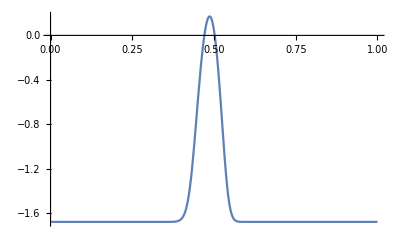

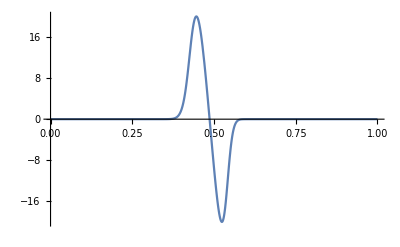

```mathematica
f[x_]=If[Abs[x]<0.9,Log[ⅇ^(-218*(-2/3-Log[1-x])^2) +ϵ] ,Log[ϵ]];
df[x_]=If[Abs[x]<.9,-(436 ⅇ^(-218 (-2/3-Log[1-x])^2) (-2/3-Log[1-x]))/(ⅇ^(-218 (-2/3-Log[1-x])^2)+ϵ),0.];
SetAttributes[f,Listable]
SetAttributes[df,Listable]
Plot[f[x],{x,a,b},PlotRange->All]
Plot[df[x],{x,a,b},PlotRange->All]
```

Let first construct a matrix A for the linear part.

```mathematica
D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
```

```mathematica
D2=NDSolve`FiniteDifferenceDerivative[Derivative[2],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
```

```mathematica
(ONN=ConstantArray[0.,{n1+1,n1+1}])//N;
(INN=IdentityMatrix[n1+1])//N;
```

```mathematica
L1Linear = (-(-1+X))/(1+X)*X^2*D2 + (2X - 3 X^2)/(1+X)*D1 //N;
L2Linear = (1-2 X^2)/(1+X)*D1 -2X*INN //N;
A=Developer`ToPackedArray[ArrayFlatten[{{ONN,INN},{L1Linear,L2Linear}}], Real];
```

As an aside we can do a quick test run of the linear equation:
(∂^2 ψ)/(∂^2 t) = Linear_terms
using the Hermite method to solve for ψ.

It might be interesting to compare Exp[ψ] where we calculated ψ as per the above, with the field we get from solving the original equation before making transformation Log[ϕ +ϵ]

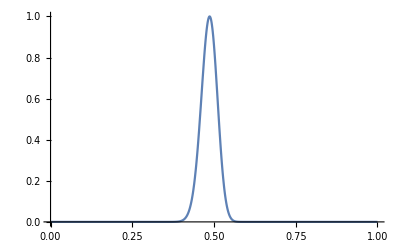

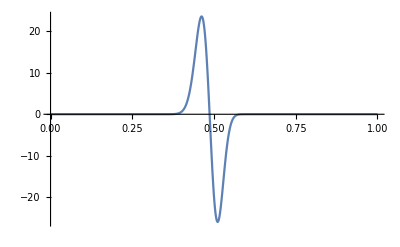

```mathematica
g[x_,t_]=If[Abs[x]<1.,If[-218*(-2/3+t-Log[1-x])^2<-583,0.,ⅇ^(-218*(-2/3+t-Log[1-x])^2)],0.];
dg[x_]=If[Abs[x]<1.,If[-218/9 (2+3 Log[1-x])^2<-583,0.,-(436 ⅇ^(-218/9 (2+3 Log[1-x])^2) (2+3 Log[1-x]))/(3 (-1+x))],0.];
SetAttributes[g,Listable]
SetAttributes[dg,Listable]
Plot[g[x,0],{x,a,b},PlotRange->All]
Plot[dg[x],{x,a,b},PlotRange->All]
```

```mathematica
(ONN=ConstantArray[0.,{n1+1,n1+1}])//N;
(INN=IdentityMatrix[n1+1])//N;
  (L1 = ((1-X)*X^2/(1+X))*D2 + (X*(2-3X)/(1+X))*D1 )//N;
(L2 = ((1-2 X^2)/(1+X))*D1  - (2X/(1+X))*INN)//N;
```

```mathematica
L2N2N=ArrayFlatten[{{ONN,INN},{L1,L2}}];
L2N2N = Developer`ToPackedArray[L2N2N, Real];
```

```mathematica
m1=100000;
tend = 1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
UOrig=ConstantArray[0.,{m1+1,2n1+2}];      (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
UOrig[[1,1;;n1+1]]=g[X,0];
UOrig[[1,n1+2;;-1]]=(1-X)*dg[X];
UOrig = Developer`ToPackedArray[UOrig, Real];
```

```mathematica
BHermOrig = Inverse[IdentityMatrix[Length[L2N2N]] -Δt/2*L2N2N + Δt^2/12*MatrixPower[L2N2N,2] ].(Δt*L2N2N ); 
BHermOrig = Developer`ToPackedArray[BHermOrig, Real];
```

```mathematica
Do[UOrig[[i+1]]=UOrig[[i]]+ BHermOrig.UOrig[[i]],
{i,1,m1}]
```

```mathematica
ψOrig=UOrig[[All,1;;n1+1]];
pOrig=UOrig[[All,n1+2;;-1]];
```

Now to write the Non-linear piece in matrix form,
Non_linear_terms  = - (-x^2+x^3)/(1+x)((∂ψ)/(∂x))^2 + (1-2 x^2)/(1+x) (∂ψ)/(∂x)(∂ψ)/(∂t) - ((∂ψ)/(∂t))^2
(B .u)*(G.u) + (H .u)*(J.u)

```mathematica
L1NonLinear1 = (X^2-X^3)/(1+X)*D1 //N;
B=Developer`ToPackedArray[ArrayFlatten[{{ONN,ONN},{L1NonLinear1,ONN}}], Real];
```

```mathematica
L1NonLinear2 = D1 //N;
G=Developer`ToPackedArray[ArrayFlatten[{{ONN,ONN},{L1NonLinear2,ONN}}], Real];
```

```mathematica
L1NonLinear3 = (1-2 X^2)/(1+X)*D1 //N;
L2NonLinear3 =  -INN //N;
H=Developer`ToPackedArray[ArrayFlatten[{{ONN,ONN},{L1NonLinear3,L2NonLinear3}}], Real];
```

```mathematica
L2NonLinear4 = INN //N;
J=Developer`ToPackedArray[ArrayFlatten[{{ONN,ONN},{ONN,L2NonLinear4}}], Real];
```

```mathematica
Uident =ConstantArray[0.,{2n1+2}];
Uident[[1;;n1+1]] =1;
```

```mathematica
BNonLinear=Developer`ToPackedArray[ArrayFlatten[{{ONN,INN},{L1NonLinear1,ONN}}], Real];
```

```mathematica
FNonLinear[t_,u_]:=(BNonLinear.u)*(G.u + Uident) + (H.u)*(J.u)
```

```mathematica
FFull[t_,u_]:= A.u  + (B.u)*(G.u) + (H.u)*(J.u)
FLinear[t_,u_]:= A.u
```

```mathematica
m1=100000;
tend = 1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
U=ConstantArray[0.,{m1+1,2n1+2}];      (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
U[[1,1;;n1+1]]=f[X];
U[[1,n1+2;;-1]]=df[X];
U = Developer`ToPackedArray[U, Real];
Δt/Δx
```

0.26354

```mathematica
FFull[T[[1]],U[[1]]];
```

```mathematica
Do[K1=Δt*FFull[T[[ν]],U[[ν]]];   (*dU/dt*)
K2=Δt*FFull[T[[ν]]+Δt/2,U[[ν]]+K1/2];
U[[ν+1]]=U[[ν]]+K2,
{ν,1,m1}]
```

```mathematica
Do[K1=Δt*FFull[T[[ν]],U[[ν]]];   (*dU/dt=F(t,U)*)
K2=Δt*FFull[T[[ν]]+Δt/2,U[[ν]]+K1/2];
K3=Δt*FFull[T[[ν]]+Δt/2,U[[ν]]+K2/2];
K4=Δt*FFull[T[[ν]]+Δt,U[[ν]]+K3];
U[[ν+1]]=U[[ν]]+(K1+2K2+2K3+K4)/6,
{ν,1,m1}]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

$Aborted

```mathematica
ψfull=U[[All,1;;n1+1]];
pfull=U[[All,n1+2;;-1]];
```

```mathematica
Manipulate[ListPlot[Transpose[{X,ψfull[[ν]]}],PlotRange->All],{ν,1,m1+1}]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{X,ψOrig[[ν]]}],PlotRange->All],
ListPlot[Transpose[{X,Exp[ψfull[[ν]]] - ϵ}],PlotRange->All, PlotStyle->Red]],{ν,1,m1+1}]
```

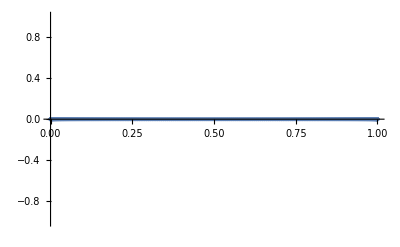

```mathematica
ListPlot[Transpose[{X,ψfull[[10000]]}],PlotRange->All]
```

```mathematica
ma = ({{-1/c^2, 0}, {0, 1}})
```

{{-1/c^2,0},{0,1}}

```mathematica
Eigenvectors[ma]
```

{{1,0},{0,1}}

```mathematica
Eigenvalues[ma]
```

{-1/c^2,1}